```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

# B_c(p1)→χ_cJ(p2, {α,β}) + W_μ(q)

```mathematica
Ebert, Faustov, Galkin, arXiv:1007.1369 [hep-ph]
```

## Init

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
<<MyPackages`ChDim`
```

```mathematica
ClearScalarProducts[];
ScalarProduct[p1, p1]=MBc^2; ScalarProduct[p2, p2]=Mcc^2; ScalarProduct[q,q]=q2;
ScalarProduct[p1,p2]=Calc[(SP[p1]+SP[p2]-SP[q])/2];
ScalarProduct[p1, q]=Calc[(SP[p1]+SP[q]-SP[p2])/2];
ScalarProduct[p2,q]=Calc[(SP[p1]-SP[p2]-SP[q])/2];
Calc[SP[#]&/@{p2+q, p1-q, p1-p2}]
```

{MBc^2,Mcc^2,q2}

```mathematica
SetOptions[ChDim, Dimensions->{
GF->-2,
a1->0, beta->0, Vbc->0, Vuq->0,
mu->0,a->0, b->0,
rhoL[_]->0, rhoT[_]->0,
fPlus[_]->0, fMinus[_]->0,
hA[_]->0, hV1[_]->0, hV2[_]->0, hV3[_]->0,
tV[_]->0, tA1[_]->0, tA2[_]->0, tA3[_]->0,
fP->1, mP->1, fV->1, mV->1,
p1->1, p2->1,q->1, MBc->1, Mcc->1,
q2->2}];
```

```mathematica
chiList = {"chi_c0", "chi_c1", "chi_c2"};
```

## Amplitudes

```mathematica
ffList={}
```

{}

```mathematica
Clear[amplitude];
amplitude::usage = "amplitude[out, |\"A\"|\"V\"] is the amplitude for Bc -> out decay, see relations (2)-(4) from the article";
amplitude[out_, "V+A"]:=amplitude[out,"V"]+amplitude[out,"A"];
```

```mathematica
Join[{1},{2}]
```

{1,2}

```mathematica
(* (19) *)
out = "chi_c0";
amplitude[out, "V"]=0;
amplitude[out, "A"]=fPlus[q2]FV[p1+p2,mu]+fMinus[q2]FV[p1-p2,mu];
ffList = DeleteDuplicates[Join[ffList,{fPlus, fMinus}]];
```

```mathematica
ChDim[amplitude[out, "A"]]
```

-0.00254665 $M

```mathematica
(* (20) *)
out = "chi_c1";
amplitude[out,"V"]=(MBc+Mcc)hV1[q2]MT[mu,a]+(hV2[q2]FV[p1,mu]+hV3[q2]FV[p2,mu])FV[q,a]/MBc;
amplitude[out, "A"]=(2I hA[q2])/(MBc+Mcc)LeviCivita[mu,a][p1,p2];
ffList = DeleteDuplicates[Join[ffList,{hV1, hV2, hV3, hA}]];
```

```mathematica
ChDim[amplitude[out, "V"]//Calc]
```

0.070615 $M

```mathematica
(* (22) *)
out = "chi_c2";
amplitude[out,"V"]=(2I tV[q2])/(MBc+Mcc)LeviCivita[mu,a][p1,p2] FV[p1,b]/MBc;
amplitude[out, "A"]=(MBc+Mcc)tA1[q2]*MT[mu,b] FV[p1,a]/MBc+
(tA2[q2]FV[p1,mu]+tA3[q2]FV[p2,mu])(FV[p1,a]FV[p1,b])/MBc^2;
ffList = DeleteDuplicates[Join[ffList,{tV, tA1, tA2, tA3}]];
```

```mathematica
ChDim[amplitude[out, "A"]//Calc]
```

2.80848 $M

```mathematica
Do[Print[{out,t}, "\t",ChDim[FCI[amplitude[out, t]]]],{out,chiList},{t,{"A","V"}}]
```

{chi_c0,A}	0.193754 $M

{chi_c0,V}	0

{chi_c1,A}	(0.+0.0209962 ⅈ) $M

{chi_c1,V}	0.501239 $M

{chi_c2,A}	0.736389 $M

{chi_c2,V}	(0.+0.0000226755 ⅈ) $M

```mathematica
amplitude[out_,"V+A"]:=amplitude[out, "V"]+amplitude[out,"A"];
Do[Print[{out,t}, "\t",ChDim[FCI[amplitude[out, t]]]],{out,chiList},{t,{"A","V", "V+A"}}]
```

{chi_c0,A}	0.655441 $M

{chi_c0,V}	0

{chi_c0,V+A}	0.194446 $M

{chi_c1,A}	(0.+0.00228651 ⅈ) $M

{chi_c1,V}	0.256804 $M

{chi_c1,V+A}	(0.257002+0.0877574 ⅈ) $M

{chi_c2,A}	0.00641998 $M

{chi_c2,V}	(0.+0.290244 ⅈ) $M

{chi_c2,V+A}	(0.0555981+0.00274612 ⅈ) $M

## Widths

```mathematica
J[a_, b_]:=PolarizationSum[a, b, p2];
J2[{a_,b_},{ca_, cb_}]:=(J[a, ca]*J[b,cb]+J[a,cb]*J[b,ca])/2-J[a,b]J[ca,cb]/3
```

```mathematica
{Calc[J2[{a,a},{ca, cb}]],
Calc[J2[{a,b},{ca, ca}]],
Calc[J2[{ca,cb},{ca, cb}]]}
```

{0,0,5}

```mathematica
Clear[outPol];
outPol["L", "P"]=(-I fP FV[p1-p2,mu]);
outPol["L","V"]=mV*fV;
outPol["L","W"]=1;
```

```mathematica
Clear[outPol2];
outPol2["L","P"]=1;
outPol2["L","V"]=PolarizationSum[mu, ci[mu], q];
outPol2["L","W"]=(FV[q, mu]FV[q,ci[mu]]-SP[q]*MT[mu, ci[mu]])*rhoT[q2]+FV[q,mu]FV[q,ci[mu]]rhoL[q2];
outPol2["H","chi_c0"]=1;
outPol2["H","chi_c1"]=PolarizationSum[a,ci[a],p2];
outPol2["H", "chi_c2"]=J2[{a,b},{ci[a],ci[b]}];
```

```mathematica
Clear[gamma];
PrintTemporary[Dynamic[{out, outL}]];
Do[
matr = GF/(√2)Vbc Vuq a1 amplitude[out, "V+A"]*outPol["L",outL];
matr = Simplify[Contract[matr]];
cmatr = ComplexConjugate[matr]/.{LorentzIndex[m_]:>LorentzIndex[ci[m]]};
matr2 = matr*cmatr*outPol2["L", outL]*outPol2["H", out];
matr2 = Simplify[Contract[matr2]];
gamma[out, outL] = Simplify[1/(2MBc)beta/(8Pi)matr2];
,{out, chiList},{outL,{"P", "V", "W"}}];
```

```mathematica
Do[
Print[{out, outL},"\t",ChDim[gamma[out, outL]]];
,{out, chiList},{outL,{"P","V","W"}}]
```

{chi_c0,P}	2.79715×10^-6 $M

{chi_c0,V}	0.0000471449 $M

{chi_c0,W}	(1.45129×10^-6)/($M)

{chi_c1,P}	-6.54857×10^-9 $M

{chi_c1,V}	3.85743×10^-8 $M

{chi_c1,W}	(1.87699×10^-7)/($M)

{chi_c2,P}	1.57973×10^-7 $M

{chi_c2,V}	-2.50903×10^-10 $M

{chi_c2,W}	-(6.04737×10^-10)/($M)

## Form Factors

```mathematica
Clear[extractFF];
extractFF::usage="extractFF[json, num]";
extractFF[json_, n_, fact_:1]:=Module[{name, data},
name = json⟦3,2,n,1,2⟧;
data = json⟦3,2,n,5,2,All,3,2⟧;
data⟦All,2⟧=fact*data⟦All,2⟧;
Return[<|"name"->name,"data"->data|>]
]
```

### χ_c(1P)

```mathematica
tab$fPlus = Import["../literatute/Ebert_FFs/chi0_fPlus.csv"];
tab$fMinus = Import["../literatute/Ebert_FFs/chi0_minusFminus.csv"];
tab$fMinus⟦All,2⟧=-tab$fMinus⟦All,2⟧;
```

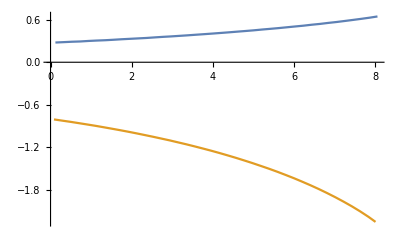

```mathematica
ListPlot[{tab$fPlus, tab$fMinus}, Joined->True]
```

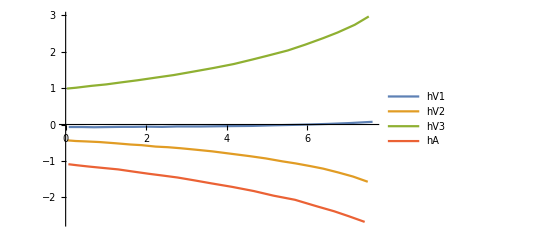

```mathematica
chic1 = Import["../literatute/Ebert_FFs/fig3_chic1_1P.json"];
tab$hV1 = extractFF[chic1,1]["data"];
tab$hV2 = extractFF[chic1,2, -1]["data"];
tab$hV3 = extractFF[chic1,3]["data"];
tab$hA = extractFF[chic1,4,-1]["data"];
ListPlot[{tab$hV1,tab$hV2,tab$hV3, tab$hA}, Joined->True, PlotLegends->{"hV1", "hV2", "hV3", "hA"}]
```

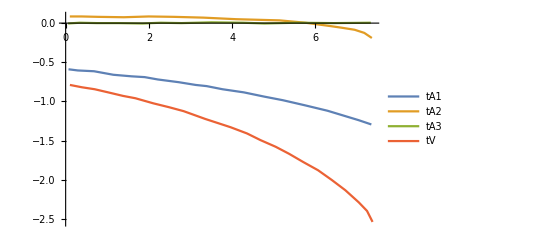

```mathematica
chic2 = Import["../literatute/Ebert_FFs/fig3_chic2_1P.json"];
tab$tA3 = extractFF[chic2, 1]["data"];
tab$tA2 = extractFF[chic2, 2]["data"];
tab$tA1 = extractFF[chic2, 3, -1]["data"];
tab$tV = extractFF[chic2, 4,-1]["data"];
ListPlot[{tab$tA1, tab$tA2, tab$tA3, tab$tV},Joined->True, PlotLegends->{"tA1", "tA2", "tA3", "tV"}, PlotRange->All]
```

### χ_c(2P)

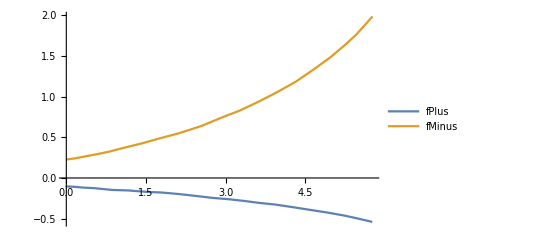

```mathematica
chic0 = Import["../literatute/Ebert_FFs/fig3_chic0_2P.json"];
tab$fPlus$2P = extractFF[chic0,1,-1]["data"];
tab$fMinus$2P = extractFF[chic0,2]["data"];
ListPlot[{tab$fPlus$2P, tab$fMinus$2P}, Joined->True, PlotLegends->{"fPlus", "fMinus"}]
```

{hV1,hV2,hA,-hV3}

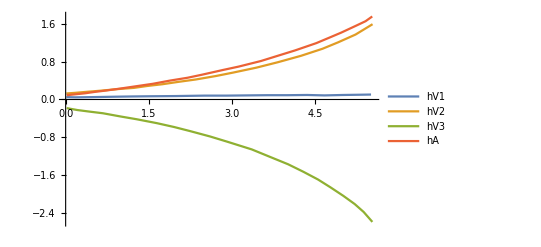

```mathematica
chic1 = Import["../literatute/Ebert_FFs/fig3_chic1_2P.json"];
chic1⟦3,2,All,1,2⟧
tab$hV1$2P = extractFF[chic1,1]["data"];
tab$hV2$2P = extractFF[chic1,2]["data"];
tab$hA$2P = extractFF[chic1,3]["data"];
tab$hV3$2P = extractFF[chic1,4,-1]["data"];
ListPlot[{tab$hV1$2P,tab$hV2$2P,tab$hV3$2P, tab$hA$2P}, Joined->True, PlotLegends->{"hV1", "hV2", "hV3", "hA"}]
```

{tA3,tA2,tA1,tV}

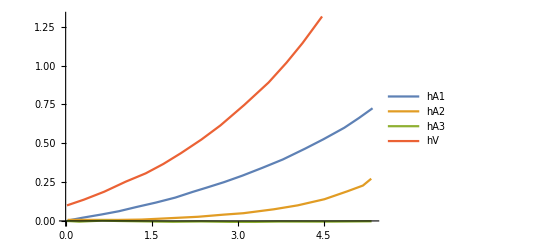

```mathematica
chic2 = Import["../literatute/Ebert_FFs/fig3_chic2_2P.json"];
Print[chic2⟦3,2,All,1,2⟧];
tab$tA3$2P = extractFF[chic2,1]["data"];
tab$tA2$2P = extractFF[chic2,2]["data"];
tab$tA1$2P = extractFF[chic2,3]["data"];
tab$tV$2P = extractFF[chic2,4]["data"];
ListPlot[{tab$tA1$2P,tab$tA2$2P,tab$tA3$2P, tab$tV$2P}, Joined->True, PlotLegends->{"hA1", "hA2", "hA3", "hV"}]
```

```mathematica
fitFunc=a0+a1 q2 + a2 q2^2+a3 q2^3;
fitParams = DeleteCases[Variables[fitFunc] ,q2]
```

{a0,a1,a2,a3}

```mathematica
ffFitRule = Table[
ff[q2_]:>Evaluate[ fitFunc/.FindFit[ToExpression["tab$"<>ToString[ff]], fitFunc,fitParams,q2]]
,{ff, ffList}];
```

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule[[i,2]]/.Power->pow]]<>";\n"
,{i,1,2}];
str
```

*fPlus=0.2735114574549966 + 0.02698177783795792*q2 + 0.0004438591230092838*pow(q2,2) + 0.00023394089715202517*pow(q2,3);
*fMinus=-0.7888608969785541 - 0.10052789894587946*q2 + 0.0028122053015600472*pow(q2,2) - 0.0015941397716725178*pow(q2,3);

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule[[i,2]]/.Power->pow]]<>";\n"
,{i,3,6}];
str
```

*hV1=-0.07249517884406438 + 0.006386114470446252*q2 - 0.0016598461472340164*pow(q2,2) + 0.00043125401922510393*pow(q2,3);
*hV2=-0.42708574288736423 - 0.08150607461417403*q2 + 0.00655250512925111*pow(q2,2) - 0.002089171872485879*pow(q2,3);
*hV3=0.9721190093276546 + 0.14785518940757297*q2 - 0.010128808927653912*pow(q2,2) + 0.0033475878397617523*pow(q2,3);
*hA=-1.0807476041824315 - 0.1250995787006434*q2 + 0.00032468802756664515*pow(q2,2) - 0.0016479191668232192*pow(q2,3);

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule[[i,2]]/.Power->pow]]<>";\n"
,{i,7,10}];
str
```

*tV=-0.7593279619789294 - 0.14373638874539618*q2 + 0.015428531108854306*pow(q2,2) - 0.0037404399820982963*pow(q2,3);
*tA1=-0.5845892322932432 - 0.05829150603138564*q2 + 0.0003828588805250468*pow(q2,2) - 0.0007578111067025861*pow(q2,3);
*tA2=0.0939174867271461 - 0.029819354099933058*q2 + 0.01373975840177015*pow(q2,2) - 0.0019524446633583286*pow(q2,3);
*tA3=-0.0020369655557486233 + 0.0033852618872049524*q2 - 0.0008299552762151167*pow(q2,2) + 0.00006460810519319177*pow(q2,3);

```mathematica
ffFitRule$2P = Table[
ff[q2_]:>Evaluate[ fitFunc/.FindFit[ToExpression["tab$"<>ToString[ff]<>"$2P"], fitFunc,fitParams,q2]]
,{ff, ffList}];
```

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule$2P⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule$2P[[i,2]]/.Power->pow]]<>";\n"
,{i,1,2}];
str
```

*fPlus=-0.1036523606752476 - 0.04296031595098163*q2 + 0.0006186521497841605*pow(q2,2) - 0.0010752967931538292*pow(q2,3);
*fMinus=0.2146487305494538 + 0.15242330361247391*q2 - 0.010551275203077543*pow(q2,2) + 0.006370594008633078*pow(q2,3);

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule$2P⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule$2P[[i,2]]/.Power->pow]]<>";\n"
,{i,3,6}];
str
```

*hV1=0.04439115389660447 + 0.019084131704071243*q2 - 0.002604726424031802*pow(q2,2) + 0.00018149830649920272*pow(q2,3);
*hV2=0.1172598023033568 + 0.12069109270869871*q2 - 0.012606920768015749*pow(q2,2) + 0.006864162691296876*pow(q2,3);
*hV3=-0.16364417143981633 - 0.22885046487359123*q2 + 0.030520612375782352*pow(q2,2) - 0.012027948054465212*pow(q2,3);
*hA=0.07973359107787653 + 0.15842249566142913*q2 - 0.005579327065777525*pow(q2,2) + 0.00560617437583373*pow(q2,3);

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule$2P⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule$2P[[i,2]]/.Power->pow]]<>";\n"
,{i,7,10}];
str
```

*tV=0.09539971009568 + 0.1323082354062854*q2 + 0.007744430814653726*pow(q2,2) + 0.0052822727875911765*pow(q2,3);
*tA1=-0.0014086383044029733 + 0.06739181582166379*q2 + 0.0036492170862357574*pow(q2,2) + 0.0016746836655900166*pow(q2,3);
*tA2=0.0017971881442419284 + 0.01760619468206874*q2 - 0.010590128853260362*pow(q2,2) + 0.0030609488394743095*pow(q2,3);
*tA3=-0.0008750946774129126 - 0.0005646397692624229*q2 - 0.0007184243134305922*pow(q2,2) + 0.0001459108759474624*pow(q2,3);

## Numbers

```mathematica
gammaTot = (6.6*10^-22 10^-3)/(0.5*10^-12);
```

```mathematica
Clear[getMcc];
(* 1P masses from PDG *)
getMcc[out_, type_:"1P"]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
(* 2P masses are chosen to fit Ebert's distributions *)
getMcc[out_, "2P"]:=Switch[out,"chi_c0", 3862MeV,"chi_c1", 3.9214,"chi_c2",3.967735]
```

```mathematica
ffRule = (ToExpression[#]->Interpolation[ToExpression["tab$"<>ToString[#]]])&/@ffList;
```

```mathematica
GeV=1; MeV=10^-3 GeV;
```

```mathematica
Clear[Ngamma];
Ngamma[out_, outL_, type_:"1P"]:=Module[{
$Mcc=getMcc[out, type],
$q2=Switch[outL,"P", mPi, "V", mV, "W",q2],
fffit = Switch[type,"1P",ffFitRule,"2P", ffFitRule$2P]
},
gamma[out, outL]//.{
beta -> √(1-((Mcc+√q2)/MBc)^2)√(1-((Mcc-√q2)/MBc)^2),
GF->1.16*10^-5 GeV^-2,fP->130MeV,fV->208MeV,
Vuq ->0.973,Vbc-> 40.8*10^-3,a1 ->1.14
}//.{MBc -> 6274.47MeV, mPi->140MeV, mV->770MeV, Mcc->$Mcc, q2->$q2}/.fffit]
```

```mathematica
10^15/1.14^2 Ngamma["chi_c0", "P"]
```

0.227085

```mathematica
10^15/1.14^2 Ngamma["chi_c1", "P"]
```

0.0128168

```mathematica
10^15/1.14^2 Ngamma["chi_c2", "P"]
```

0.392902

```mathematica
distEE["chi_c0"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic0_1P.json"], 1]["data"];
distEE["chi_c1"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic1_1P.json"], 1]["data"];
distEE["chi_c2"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic2_1P.json"], 1]["data"];
```

```mathematica
distEE["chi_c0","2P"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic0_2P.json"], 1]["data"];
distEE["chi_c1","2P"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic1_2P.json"], 1]["data"];
distEE["chi_c2","2P"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic2_2P.json"], 1]["data"];
```

```mathematica
out = "chi_c0";
root=ReadList["../c++/build/"<>out<>"_en.txt", {Number,Number,Number}];
root⟦All,2;;3⟧*=Max[distEE[out]⟦All,2⟧]/Max[root⟦All,2⟧];
Show[
ListPlot[distEE[out], PlotStyle->Red],
Plot[0.8 10^13/(40.8*10^-3)^2 Ngamma[out,"W"]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}, {q2, 0.2,8}],
ListPlot[root⟦All,1;;2⟧, PlotMarkers->"o"]
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out]
```

-Graphics-

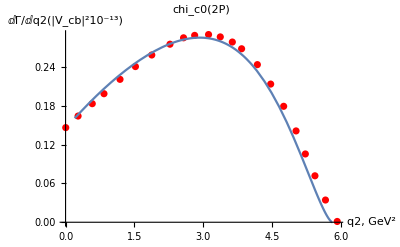

```mathematica
out = "chi_c0";
(*
root=ReadList["../c++/build/"<>out<>"_en.txt", {Number,Number,Number}];
root⟦All,2;;3⟧*=Max[distEE[out]⟦All,2⟧]/Max[root⟦All,2⟧];
*)
Show[
ListPlot[distEE[out,"2P"], PlotStyle->Red],
Plot[0.82 10^13/(40.8*10^-3)^2 Ngamma[out,"W","2P"]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}, {q2, 0.2,8}]
(*,ListPlot[root⟦All,1;;2⟧, PlotMarkers->"o"]*)
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out<>"(2P)"]
```

```mathematica
out = "chi_c1";
root=ReadList["../c++/build/"<>out<>"_en.txt", {Number,Number,Number}];
root⟦All,2;;3⟧*=Max[distEE[out]⟦All,2⟧]/Max[root⟦All,2⟧];
Show[
ListPlot[distEE[out], PlotStyle->Red],
Plot[0.84 10^13/(40.8*10^-3)^2 Ngamma[out,"W"]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}, {q2, 0.2,8}],
ListPlot[root⟦All,1;;2⟧, PlotMarkers->"o"]
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out]
```

-Graphics-

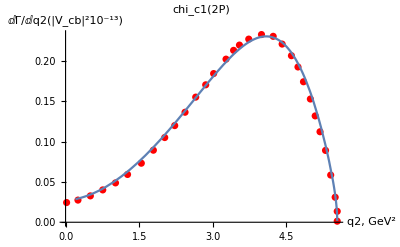

```mathematica
out = "chi_c1";
(*
root=ReadList["../c++/build/"<>out<>"_en.txt", {Number,Number,Number}];
root⟦All,2;;3⟧*=Max[distEE[out]⟦All,2⟧]/Max[root⟦All,2⟧];
*)
Show[
ListPlot[distEE[out,"2P"], PlotStyle->Red],
Plot[0.8 10^13/(40.8*10^-3)^2 Ngamma[out,"W","2P"]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}, {q2, 0.2,8}]
(*,ListPlot[root⟦All,1;;2⟧, PlotMarkers->"o"]*)
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out<>"(2P)"]
```

```mathematica
out = "chi_c2";
root=ReadList["../c++/build/"<>out<>"_en.txt", {Number,Number,Number}];
root⟦All,2;;3⟧*=Max[distEE[out]⟦All,2⟧]/Max[root⟦All,2⟧];
Show[
ListPlot[distEE[out], PlotStyle->Red],
Plot[0.82 10^13/(40.8*10^-3)^2 Ngamma[out,"W"]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}, {q2, 0.2,8}],
ListPlot[root⟦All,1;;2⟧, PlotMarkers->"o"]
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out]
```

-Graphics-

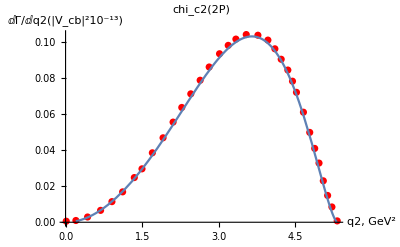

```mathematica
out = "chi_c2";
(*
root=ReadList["../c++/build/"<>out<>"_en.txt", {Number,Number,Number}];
root⟦All,2;;3⟧*=Max[distEE[out]⟦All,2⟧]/Max[root⟦All,2⟧];
*)
Show[
ListPlot[distEE[out,"2P"], PlotStyle->Red],
Plot[0.84 10^13/(40.8*10^-3)^2 Ngamma[out,"W","2P"]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}, {q2, 0.2,8}]
(*,ListPlot[root⟦All,1;;2⟧, PlotMarkers->"o"]*)
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out<>"(2P)"]
```

```mathematica
6274.47MeV-√(distEE[out,"2P"]⟦-1,1⟧)//InputForm
```

3.9677353230797

```mathematica
distEE[out,"2P"]⟦-1,1⟧
```

5.32102